## Байдук Я. А.

## Лабораторная работа №2 : Символьные вычисления в системе Mathematica

## 2.1

### 1. Придумайте и определите символьное выражение содержащее не менее трех слагаемых, причём хотя бы одно из них должно быть рациональным выражением

```mathematica
fun1= x^2+y^2+(x+y)^3+(x*y*(4*x^2+6*x+8*y))/(2*x^2+4*y+3*x);
```

```mathematica
Expand[fun1](*Раскрыла скобки и представил ввиде суммы*)
```

x^2+x^3+3 x^2 y+y^2+3 x y^2+y^3+(6 x^2 y)/(3 x+2 x^2+4 y)+(4 x^3 y)/(3 x+2 x^2+4 y)+(8 x y^2)/(3 x+2 x^2+4 y)

```mathematica
Factor[fun1](*Вынеса за скобки общ множитель и представил в виде произведения*)
```

(x+y)^2 (1+x+y)

```mathematica
Together[fun1](*Собирает из простых частей сумму*)
```

x^2+x^3+2 x y+3 x^2 y+y^2+3 x y^2+y^3

```mathematica
Apart[fun1](*Разложила на простые дроби*)
```

x^2 (1+x)+x (2+3 x) y+(1+3 x) y^2+y^3

```mathematica
Cancel[fun1](*Сократила числители и заменатели*)
```

x^2+2 x y+y^2+(x+y)^3

```mathematica
Simplify[fun1](*Упростила выражение*)
```

(x+y)^2 (1+x+y)

### 2. Приведите своё выражение к общему знаменателю и с помощью функции Numerator определите числитель полученного выражения обозначив его другим именем. С помощью функции Collect представьте это выражение в виде полинома по степеням x или y. Определите максимальную степень n одной из переменных, например х и коэффициент х^n. Используйте функции Exponent и Coefficient

```mathematica
fun2=Numerator[Together[fun1]](*Привёла выражение к общему знаменателю*)
```

x^2+x^3+2 x y+3 x^2 y+y^2+3 x y^2+y^3

```mathematica
Collect[fun2,x](*Представила в виде полинома по степеням х*)
```

```mathematica
x^3+y^2+y^3+x^2 (1+3 y)+x (2 y+3 y^2)
```

```mathematica
Exponent[fun2,x](*Максимальная степень переменной х*)
```

3

```mathematica
Coefficient[fun2,x,Exponent[fun2,x]](*Коэффициент многочлена с наибольшей степенью переменной х*)
```

1

```mathematica
Coefficient[fun2,x,2](*Коэфициент многочлена при переменной х^2*)
```

1+3 y

```mathematica
CoefficientList[fun2,x](*Список коэффициентов переменной х*)
```

{y^2+y^3,2 y+3 y^2,1+3 y,1}

## 2.2

### 1. С помощью функции D вычислите производную функции x^ncos(x)

```mathematica
D[x^n*Cos[x], x](*Вычислил производную функции*)
```

n x^(-1+n) Cos[x]-x^n Sin[x]

### 2. Вычислите следующие производные: d/dx (ax^3+2 x^2); d^3/dx^3(4 x^2-5x+8-3/x); d^5/(dx^3*dy^2) (x^3*y^2+3 x^2)

```mathematica
(*Вычислил неколько производных*)
```

```mathematica
D[a*x^3+2 x^2,x]
```

4 x+3 a x^2

```mathematica
D[4 x^2-5x+8-3/x,{x,3}]
```

18/x^4

```mathematica
D[x^3*y^2+3 x^2,{x,3},{y,2}]
```

12

### 3. Используя функцию Integrate вычислите интеграл: ∫dx/(x^2-1)

```mathematica
Integrate[1/(x^2-1),x](*Проинтегрировал функцию*)
```

1/2 Log[1-x]-1/2 Log[1+x]

### 4. Вычислите интегралы, затем продифференцируйте полученные выражения и убедитесь в том, что получаемые результаты совпадают подынтегральными выражениями: ∫x^3/(x^2+1)dx; ∫1/(x^3+1)dx

```mathematica
(*Вычислил интегралы, а затем с помощью производной убедился в совпадении подынтегральных выражений*)
```

```mathematica
Integrate[x^3/(x^2+1),x]
```

x^2/2-1/2 Log[1+x^2]

```mathematica
Simplify[D[x^2/2-1/2*Log[1+x^2],x]]
```

x^3/(1+x^2)

```mathematica
Integrate[1/(x^3+1),x]
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
Simplify[D[ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2],x]]
```

1/(1+x^3)

### 5. Вычислите определённый интеграл: ∫_1^4 (5x-2 √x+32/x^3)dx

```mathematica
Integrate[5x-2 √x+32/x^3,{x,1,4}](*Вычислила определённый интеграл*)
```

259/6

### 6. Вычислите интегралы: ∫_0^1 (1+x^4)^(1/3)dx; ∫_0^1. (1+x^4)^(1/3)dx(Обратить внимание на действительное число “1.” Сравнить полученные результаты)

```mathematica
Integrate[(1+x^4)^(1/3),{x,0,1}](*Гипергеометрическая функция*)
```

Hypergeometric2F1[-1/3,1/4,5/4,-1]

```mathematica
Integrate[(1+x^4)^(1/3),{x,0,1.}](*Автоматически вычисляет только с действительным числом*)
```

1.05753

## 2.3

```mathematica
1. Используя функцию Solve,решить уравнение: ax^4+x^2+3=0
```

```mathematica
Solve[ax^4+x^2+3==0,x](*Решила линейное уравнение*)
```

{{x→-√(-3-ax^4)},{x→√(-3-ax^4)}}

```mathematica
2. Найти точное решение системы уравнений: {{{x^2+y=1}, {y^2-x^2=2}}
```

```mathematica
Solve[x^2+y==1&&y^2-x^2==2,{x,y},Reals](*Решила систему уравнений и получил мн действительных чисел*)
```

{{x→-√(1/2 (3+√13)),y→1+1/2 (-3-√13)},{x→√(1/2 (3+√13)),y→1+1/2 (-3-√13)}}

```mathematica
3. Решить систему уравнений:  {{{x^2-y^2=1}, {y^3+x=5}}
```

```mathematica
NSolve[x^2-y^2==1&&y^3+x==5,{x,y}](*Просто решила систему уравнений*)
```

{{x→-0.928941-1.39823 ⅈ,y→-0.788459-1.64735 ⅈ},{x→-0.928941+1.39823 ⅈ,y→-0.788459+1.64735 ⅈ},{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285},{x→1.1236-1.05808 ⅈ,y→-0.913899+1.30087 ⅈ},{x→1.1236+1.05808 ⅈ,y→-0.913899-1.30087 ⅈ}}

```mathematica
4. Найти общие решения дифференциальных уравнений, используя функцию DSolve: y'(x)-y(x)tg(x)=x; y'(x)+y(x)tg(x)=1/cos(x). Самостоятельно задайте граничные условия и найдите соответствующие им частные решения. Постройте их графики
```

```mathematica
DSolve[y'[x]-y[x]*Tan[x]==x,y[x],x](*Получила общее решение 1-го дифф уравнения*)
```

{{y[x]→C[1] Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

```mathematica
DSolve[y'[x]+y[x]*Tan[x]==1/Cos[x],y[x],x](*Получил общее решение 2-го дифф уравнения*)
```

{{y[x]→C[1] Cos[x]+Sin[x]}}

```mathematica
func1=DSolve[{y'[x]-y[x]*Tan[x]==x,y[0]==1},y[x],{x,-10,10}](*Задал граничные условия для 1-го дифф уравнения*)
```

{{y[x]→1+x Tan[x]}}

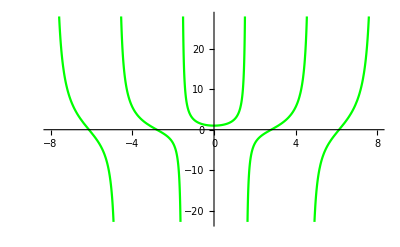

```mathematica
Plot[Evaluate[y[x]/.func1],{x,-8,8},PlotStyle->Green](*Построил соответствующий график для 1-го дифф уравнения*)
```

```mathematica
func2=DSolve[{y'[x]+y[x]*Tan[x]==1/Cos[x],y[0]==1},y[x],{x,-10,10}](*Задал граничные условия для 2-го дифф уравнения*)
```

{{y[x]→Cos[x]+Sin[x]}}

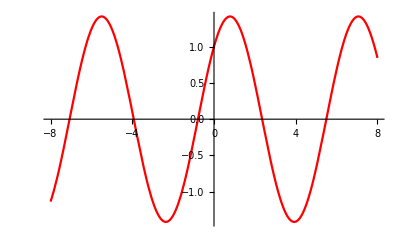

```mathematica
Plot[Evaluate[y[x]/.func2],{x,-8,8},PlotStyle->Red](*Построил соответствующий график для 2-го дифф уравнения*)
```

```mathematica
5.Самостоятельно выбрав граничные условия, найдите решение дифференциального уравнения в символьном  виде: y''(x)-y'(x)+x*y(x)=0. 
Затем  с помощью функции NDSolve найдите численное решение этого уравнения. Интервал изменения х выберите самостоятельно. На 
одной координатной плоскости постройте графики численного и символьного решений и покажите,
что они совпадают
```

```mathematica
f=DSolve[y''[x]-y'[x]+x*y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(x/2) AiryAi[-(-1)^(1/3) (1/4-x)] C[1]+ⅇ^(x/2) AiryBi[-(-1)^(1/3) (1/4-x)] C[2]}}

```mathematica
f1=FullSimplify[DSolve[{y''[x]-y'[x]+x*y[x]==0,y'[0]==0,y[0]==1},y[x],x]](*Задала граничные условия и нашёл решение в символьном виде*)
```

{{y[x]→1/2 ⅇ^(x/2) π ((AiryAi[1/4]-2 AiryAiPrime[1/4]) AiryBi[1/4-x]-AiryAi[1/4-x] (AiryBi[1/4]-2 AiryBiPrime[1/4]))}}

```mathematica
f2=NDSolve[{y''[x]-y'[x]+x*y[x]==0,y'[0]==0,y[0]==1},y[x],{x,-6,12}](*Нашла численное решение*)
```

{{y[x]→InterpolatingFunction[…][x]}}

```mathematica
graphic=Show[Plot[Evaluate[y[x]/.f1],{x,-2,7},PlotStyle->Black],Plot[Evaluate[y[x]/.f2],{x,-2,7},PlotStyle->{Dashed,Green}]]
```

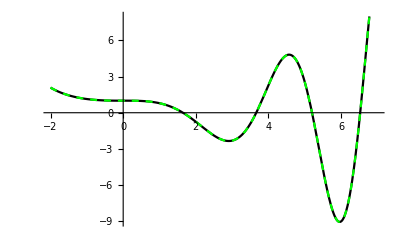

```mathematica
(*На одной коорд плоскости отобразила численное и символьное решение данного ур-я. Из графиков ниже видно, что эти решения совпадают*)
```